## 2.4 Homoclinic bifurcation

#### a)

```mathematica
Solve[{μ*x+y-x^2==0,-x + μ*y + 2*x^2==0},{x,y}]
```

{{x→0,y→0},{x→(1+μ^2)/(2+μ),y→(1-2 μ+μ^2-2 μ^3)/(2+μ)^2}}

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

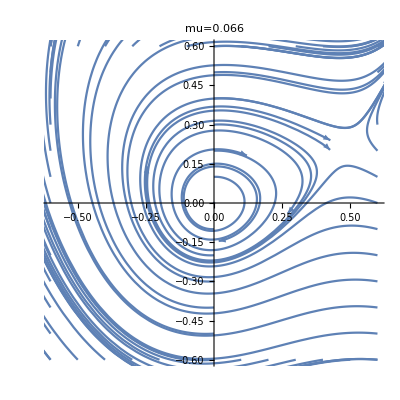

```mathematica
(*Check different values of μ and found that μ=0.066 gives a 
homoclinical bifurcation*)
tEnd = 10;
tStart = 0;
xMin=-0.6;
xMax=0.6;
yMin=-0.6;
yMax=0.6;
systemSolver[x0_, y0_]=NDSolve[{x'[t]==μ*x[t]+y[t]-x[t]^2,y'[t]==-x[t]+μ*y[t]+2 x[t]^2,x[0]==x0,y[0]==y0}/. μ->0.066,{x,y},{t,tStart,tEnd}];

table1 =Table[{0,y},{y,yMin,yMax,0.1}];table2 = Table[{xMin,y},{y,yMin,yMax,0.1}];table3=Table[{xMax,y},{y,yMin,yMax,0.1}];table4 =Table[{x,yMin},{x,xMin,xMax,0.1}];table5 =Table[{x,yMax},{x,xMin,xMax,0.1}];
initialCondition=Join[table1,table2,table3,table4,table5];

Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/. systemSolver[initialCondition[[i,1]],initialCondition[[i,2]]]],{t,tStart,tEnd},PlotRange->{{xMin,xMax},{yMin,yMax}}],{i,Length[initialCondition]}]/. Line[x_]:>{Arrowheads[{0.,0.04, 0.04, 0.04, 0.}],Arrow[x]}, PlotLabel-> "mu=0.066"]
```

#### c)

```mathematica
ODEs = {x'[t]==u*x[t], y'[t]==s*y[t],x[0]==γ,y[0]==1 };
sol = DSolve[ODEs,{x[t],y[t]},t];
Solve[(x[t]/.sol[[1]][[1]])==1,t]
```

{{t→ConditionalExpression[(2 ⅈ π C[1]+Log[1/γ])/u, C[1]∈ℤ]}}

```mathematica
(*answer is log(1/γ)/u*)
```

### d)

```mathematica
fixedPoints = Solve[{μ*x+y-x^2==0,-x + μ*y + 2*x^2==0},{x,y}];
xSaddlePoint = fixedPoints[[2]][[1]]
```

x→(1+μ^2)/(2+μ)

```mathematica
(*taking the derivative of xDot with respect to x and then y*)
xDot[x_, y_, μ_] := μ x+y−x^2;
yDot[x_,y_,μ_]:=-x+μ y +2 x^2;
derivativeXDotx = D[xDot[x,y,μ],x]
derivativeXDoty= D[xDot[x,y,μ],y]
```

-2 x+μ

1

```mathematica
(*taking the derivative of yDot with respect to x and then y*)
derivativeYDotx = D[yDot[x,y,μ],x]
derivativeYDoty = D[yDot[x,y,μ],y]
```

-1+4 x

μ

```mathematica
(*From the above partial derivatives, we create the jacobian 
matrix, with the saddle x as the x parameter*)
jacobian = {{derivativeXDotx/.xSaddlePoint,derivativeXDoty},{derivativeYDotx/.xSaddlePoint,derivativeYDoty}}
```

{{μ-(2 (1+μ^2))/(2+μ),1},{-1+(4 (1+μ^2))/(2+μ),μ}}

```mathematica
eigenVals  = Eigenvalues[jacobian]
```

{(-1+2 μ-√(5+9 μ^2+4 μ^3+μ^4))/(2+μ),(-1+2 μ+√(5+9 μ^2+4 μ^3+μ^4))/(2+μ)}

```mathematica
answer = eigenVals[[2]]
```

(-1+2 μ+√(5+9 μ^2+4 μ^3+μ^4))/(2+μ)